```mathematica
alphas[mu_,X_]:=
(4*Pi*(1. - (64.*Log[Log[0.777632*mu^2*X^2]])/(81.*Log[0.777632*mu^2*X^2])))/
	 (9.*Log[0.777632*mu^2*X^2])
```

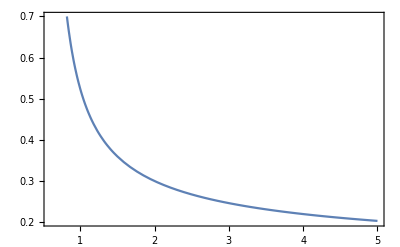

```mathematica
Plot[alphas[lbar*3.,1.],{lbar,0.6,5},
Frame->True,PlotRange->{0.2,0.7}]
```

```mathematica
dasdmub[mu_,X_]=Evaluate[D[alphas[mu,X],mu]]//FullSimplify
```

(-2.20644-2.79253 Log[0.777632 mu^2 X^2]+4.41288 Log[Log[0.777632 mu^2 X^2]])/(mu Log[0.777632 mu^2 X^2]^3)

```mathematica
dasdmub[2.4,2*0.5]
```

-0.56929

```mathematica
Plot[Evaluate[D[alphas[lbar*3.,1.],lbar]],{lbar,0.6,5},
Frame->True,PlotRange->{0.2,0.7}]
```

-Graphics-

```mathematica
alphas[0.8*3, 2.*2.0]
```

0.23906

```mathematica
(* Definitions from 2307.08734, Supp. Mat. Table I *)
```

```mathematica
a11=-2;
a21=-1;
a22=-3;
a23=-5.0021;
3*(as/Pi)^2(a21 Log[3 as/Pi]+a22 Log[X/2]+a23)//PowerExpand//N//Expand
```

-0.874364 as^2-0.303964 as^2 Log[as]-0.911891 as^2 Log[X]

```mathematica
+1.831-2.706
```

-0.875

```mathematica
(* Matches Oleg's pQCD.py file, when X = Lbar/muQ *)
```